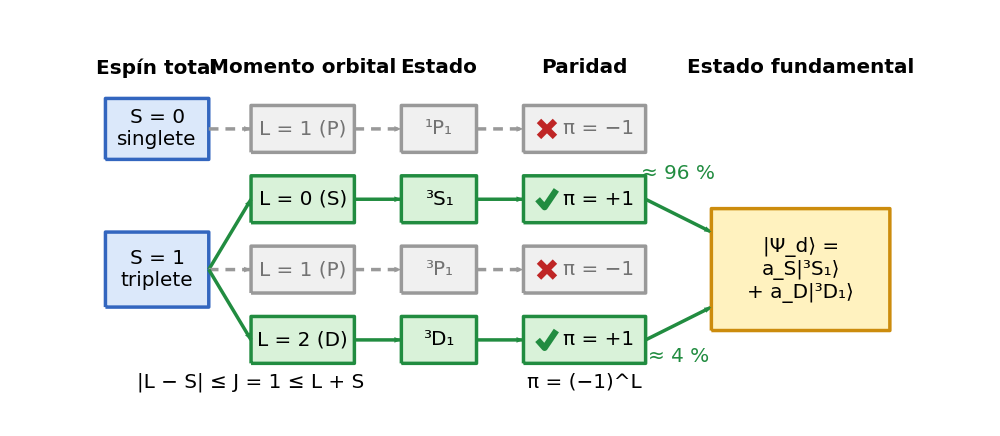

```mathematica
(*----------Parámetros globales----------*)fs=20;   (*tamaño de fuente único para todo el gráfico*)

verde=RGBColor[0.85,0.95,0.85];verdeB=RGBColor[0.13,0.55,0.25];
azul=RGBColor[0.86,0.91,0.98];azulB=RGBColor[0.20,0.40,0.75];
gris=GrayLevel[0.94];grisB=GrayLevel[0.60];grisT=GrayLevel[0.45];
rojo=RGBColor[0.75,0.15,0.15];
oro=RGBColor[1.0,0.95,0.75];oroB=RGBColor[0.80,0.55,0.05];

(*----------Geometría de las columnas----------*)
{xS,wS}={1.4,2.2};    (*espín*)
{xL,wL}={4.5,2.2};    (*momento orbital*)
{xE,wE}={7.4,1.6};    (*estado espectroscópico*)
{xP,wP}={10.5,2.6};   (*paridad*)
{xF,wF}={15.1,3.8};   (*estado fundamental*)

(*----------Funciones auxiliares----------*)
txt[expr_,pos_,col_:Black]:=Text[Style[expr,fs,col],pos];

caja[{xc_,yc_},{w_,h_},fondo_,borde_]:={EdgeForm[{AbsoluteThickness[2.5],borde}],fondo,Rectangle[{xc-w/2,yc-h/2},{xc+w/2,yc+h/2},RoundingRadius->0.15]};

flecha[p1_,p2_,col_,dash_]:={col,AbsoluteThickness[2.5],AbsoluteDashing[dash],Arrowheads[0.02],Arrow[{p1,p2}]};

visto[{x_,y_}]:={verdeB,AbsoluteThickness[4.5],CapForm["Round"],JoinForm["Round"],Line[{{x-0.2,y},{x-0.05,y-0.17},{x+0.2,y+0.2}}]};

aspa[{x_,y_}]:={rojo,AbsoluteThickness[4.5],CapForm["Round"],Line[{{x-0.17,y-0.17},{x+0.17,y+0.17}}],Line[{{x-0.17,y+0.17},{x+0.17,y-0.17}}]};

termino[s_,l_,j_]:=Row[{Superscript["",s],Subscript[l,j]}];
ket[e_]:=Row[{"|",e,"⟩"}];

(*----------Datos:{y,S,L,letra} para J=1----------*)
filas={{5.7,0,1,"P"},{4.2,1,0,"S"},{2.7,1,1,"P"},{1.2,1,2,"D"}};

fila[{y_,s_,l_,letra_}]:=Module[{ok,fondo,borde,col,dash,ys},ok=EvenQ[l];(*paridad (-1)^L=+1*)fondo=If[ok,verde,gris];
borde=If[ok,verdeB,grisB];
col=If[ok,Black,grisT];
dash=If[ok,{},{7,5}];
ys=If[s==0,5.7,2.7];
{flecha[{xS+wS/2,ys},{xL-wL/2,y},borde,dash],caja[{xL,y},{wL,1.0},fondo,borde],txt[Row[{"L = ",l," (",letra,")"}],{xL,y},col],flecha[{xL+wL/2,y},{xE-wE/2,y},borde,dash],caja[{xE,y},{wE,1.0},fondo,borde],txt[termino[2 s+1,letra,1],{xE,y},col],flecha[{xE+wE/2,y},{xP-wP/2,y},borde,dash],caja[{xP,y},{wP,1.0},fondo,borde],If[ok,visto[{xP-0.8,y}],aspa[{xP-0.8,y}]],txt[Row[{"π = ",If[ok,"+1","−1"]}],{xP+0.3,y},col],If[ok,flecha[{xP+wP/2,y},{xF-wF/2,If[l==0,3.5,1.9]},verdeB,{}],{}]}];

(*----------Diagrama----------*)
diagrama=Graphics[{(*cabeceras de columna*)txt[Style["Espín total",Bold],{xS,7.0}],txt[Style["Momento orbital",Bold],{xL,7.0}],txt[Style["Estado",Bold],{xE,7.0}],txt[Style["Paridad",Bold],{xP,7.0}],txt[Style["Estado fundamental",Bold],{xF,7.0}],(*espín total*)caja[{xS,5.7},{wS,1.3},azul,azulB],txt[Column[{Row[{"S = ",0}],"singlete"},Center],{xS,5.7}],caja[{xS,2.7},{wS,1.6},azul,azulB],txt[Column[{Row[{"S = ",1}],"triplete"},Center],{xS,2.7}],(*los cuatro estados con J=1*)fila/@filas,(*estado fundamental*)caja[{xF,2.7},{wF,2.6},oro,oroB],txt[Column[{Row[{ket[Subscript["Ψ","d"]]," ="}],Row[{Subscript["a","S"],ket[termino[3,"S",1]]}],Row[{"+ ",Subscript["a","D"],ket[termino[3,"D",1]]}]},Center],{xF,2.7}],txt[Row[{"≈ 96 %"}],{12.5,4.75},verdeB],txt[Row[{"≈ 4 %"}],{12.5,0.85},verdeB],(*reglas que generan cada columna*)txt["|L − S| ≤ J = 1 ≤ L + S",{3.4,0.3}],txt[Row[{"π = ",Superscript["(−1)","L"]}],{xP,0.3}]},ImageSize->1000,AspectRatio->7.6/17.4,PlotRange->{{0,17.4},{0,7.6}},PlotRangePadding->None,Background->White]
```